# Systems of Linear Ordinary Differential Equations

To go through the work for the following lab, go to: 

http://demonstrations.wolfram.com/HomogeneousLinearSystemOfCoupledDifferentialEquations/

## Background

The demonstration investigates the following system of differential equations:

dx/dt = ax + by

dy/dt = cx + dy

for some fixed constants, a,b,c, & d.

The graphical (red) solution curve is plotted in the xy-plane.  All curves have a critical point at (0,0) (which is where y'=0 and x'=0).  We will investigate the behavior of the solution curve as t→∞.

(1)  For consistency, move the point on the curve to as close to (0.5,0.5) as you can (if the point is not already there).
(2) You can change all 4 fixed constants to see different curves.

## Part 1: Spirals

### Part A: Outward!

(i) Keeping the movable point on the curve to as close to (0.5,0.5) as you can, find values of a,b,c, & d that make your curve look like a spiral that goes around (0,0) at least 3 times where the arrows point away from (0,0).
a = .5
b= -.75
c = 1
d = -.33

(ii) Use DSolve (code below is provided once you replace the constants) to find solution functions for x(t) and y(t).

```mathematica
a=.5
b=-.75
c=1
d=-.33
```

0.5

-0.75

1

-0.33

```mathematica
DSolve[{x'[t]==a*x[t]+b*y[t],y'[t]==c*x[t]+d*y[t],x[0]==0.5,y[0]==0.5},{x[t],y[t]},t]
```

{{x[t]→(-0.220361+8.2528×10^-17 ⅈ) ((-2.269-8.49768×10^-16 ⅈ) ⅇ^(0.085 t) Cos[0.760115 t]+(1.+0. ⅈ) ⅇ^(0.085 t) Sin[0.760115 t]),y[t]→0.5 (1. ⅇ^(0.085 t) Cos[0.760115 t]+(0.76962+1.43882×10^-16 ⅈ) ⅇ^(0.085 t) Sin[0.760115 t])}}

```mathematica
Simplify[%]
```

{{x[t]→ⅇ^(0.085 t) (0.5 Cos[0.760115 t]-(0.220361-8.2528×10^-17 ⅈ) Sin[0.760115 t]),y[t]→ⅇ^(0.085 t) (0.5 Cos[0.760115 t]+(0.38481+7.19408×10^-17 ⅈ) Sin[0.760115 t])}}

(iii) Your answer may have imaginary numbers in it, but you should see that essentially, the numbers multiplied by i are 0.  Assuming that all of these numbers multiplied by i are EXACTLY zero (if you have them), define Mathematica functions (call them x1A & y1A) that represent your solutions.  Plot them together on the same set of axes with the horizontal axis representing t.  What is happening to the states of the differential equation as t→∞?
x[t] = ⅇ^(0.085 t) (0.5 Cos[0.760115 t]-(0.220361) Sin[0.760115 t])
y[t]=ⅇ^(0.085 t) (0.5 Cos[0.760115 t]+(0.38481) Sin[0.760115 t])

```mathematica
x= E^(.085 t)(.5 Cos[0.76011 t]-.220361 Sin[.76011 t])
```

ⅇ^(0.085 t) (0.5 Cos[0.76011 t]-0.220361 Sin[0.76011 t])

```mathematica
y= E^(.085 t)(.5 Cos[0.76011 t]+.38481  Sin[.76011 t])
```

ⅇ^(0.085 t) (0.5 Cos[0.76011 t]+0.38481 Sin[0.76011 t])

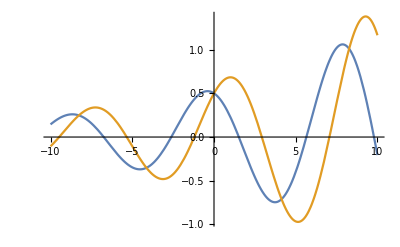

```mathematica
Plot[{x,y},{t,-10,10}]
```

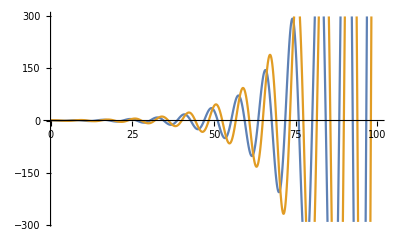

```mathematica
Plot[{x,y},{t,0,100}]
```

The amplitude of the curve is increasing for both curves as t approaches ∞.  This makes sense because the only thing that is controlling the trend amplitude (overall) is the E term. The period is also decreasing.

### Part B: Inward!

(i) Keeping the movable point on the curve to as close to (0.5,0.5) as you can, find values of a,b,c, & d that make your curve look like a spiral that goes around (0,0) at least 3 times where the arrows point toward (0,0).

```mathematica
a1=-.5
b1=.75
c1=-1
d1=.33
```

-0.5

0.75

-1

0.33

(ii) Use DSolve (as with Part 1A) to find solution functions for x(t) and y(t).

```mathematica
DSolve[{x'[t]==a1*x[t]+b1*y[t],y'[t]==c1*x[t]+d1*y[t],x[0]==0.5,y[0]==0.5},{x[t],y[t]},t]
```

{{x[t]→0.5 ⅇ^(-0.085 t) (1. Cos[0.760115 t]+(0.440723+1.65056×10^-16 ⅈ) Sin[0.760115 t]),y[t]→0.5 ⅇ^(-0.085 t) (1. Cos[0.760115 t]-(0.76962-1.43882×10^-16 ⅈ) Sin[0.760115 t])}}

(iii) As in the previous problem, your answer may have imaginary numbers in it, but you should see that essentially, the numbers multiplied by i are 0.  Assuming that all of these numbers multiplied by i are EXACTLY zero (if you have them), define Mathematica functions (call them x1B & y1B) that represent your solutions.  Plot them together on the same set of axes with the horizontal axis representing t.  What is happening to the states of the differential equation as t→∞?

```mathematica
x=0.5 ⅇ^(-0.085 t) (Cos[0.76012t]+(0.4407) Sin[0.76012 t])
```

0.5 ⅇ^(-0.085 t) (Cos[0.76012 t]+0.4407 Sin[0.76012 t])

```mathematica
y=0.5 ⅇ^(-0.085 t) (Cos[0.76012t]-(0.7696) Sin[0.76012 t])
```

0.5 ⅇ^(-0.085 t) (Cos[0.76012 t]-0.7696 Sin[0.76012 t])

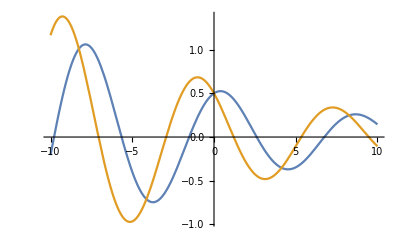

```mathematica
Plot[{x,y},{t,-10,10}]
```

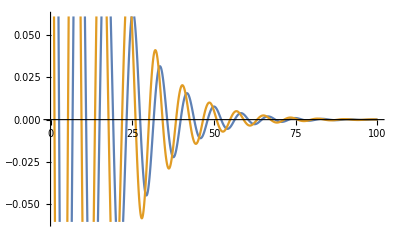

```mathematica
Plot[{x,y},{t,0,100}]
```

The amplitude of the curves becomes very small as t approaches ∞.  This makes sense because the exponent on E is approaching 0.  The period also becomes longer as t approaches ∞.

## Part 2: Circles & Ovals

(i) Keeping the movable point on the curve to as close to (0.5,0.5) as you can, find values of a,b,c, & d that make your curve look like an oval or circle that has (0,0) near the “center.”

```mathematica
a2=.45
b2=-1
c2=1
d2=-.45
```

0.45

-1

1

-0.45

(ii) Use DSolve (as with Part 1A) to find solution functions for x(t) and y(t).

```mathematica
Clear[x,y]
```

```mathematica
DSolve[{x'[t]==a2*x[t]+b2*y[t],y'[t]==c2*x[t]+d2*y[t],x[0]==0.5,y[0]==0.5},{x[t],y[t]},t]
```

{{x[t]→(0.5+2.46519×10^-32 ⅈ) ((1.+0. ⅈ) ⅇ^(2.77556×10^-17 t) Cos[0.893029 t]-(0.615882+4.79205×10^-17 ⅈ) ⅇ^(2.77556×10^-17 t) Sin[0.893029 t]),y[t]→(0.5+0. ⅈ) ((1.+0. ⅈ) ⅇ^(2.77556×10^-17 t) Cos[0.893029 t]+(0.615882+2.04561×10^-17 ⅈ) ⅇ^(2.77556×10^-17 t) Sin[0.893029 t])}}

```mathematica
Simplify[%]
```

{{x[t]→ⅇ^(2.77556×10^-17 t) ((0.5+2.46519×10^-32 ⅈ) Cos[0.893029 t]-(0.307941+2.39602×10^-17 ⅈ) Sin[0.893029 t]),y[t]→ⅇ^(2.77556×10^-17 t) (0.5 Cos[0.893029 t]+(0.307941+1.02281×10^-17 ⅈ) Sin[0.893029 t])}}

(iii) Again, your answer may have imaginary numbers in it, but you should see that essentially, the numbers multiplied by i are 0.  Assuming that all of these numbers multiplied by i are EXACTLY zero (if you have them), define Mathematica functions (call them x2 & y2) that represent your solutions.  Plot them together on the same set of axes with the horizontal axis representing t.  What is happening to the states of the differential equation as t→∞?

```mathematica
x=(0.5) Cos[0.893 t]-(0.6159)  Sin[0.893 t]
```

0.5 Cos[0.893 t]-0.6159 Sin[0.893 t]

```mathematica
y=(0.5) Cos[0.893 t]+(0.6159)  Sin[0.893 t]
```

0.5 Cos[0.893 t]+0.6159 Sin[0.893 t]

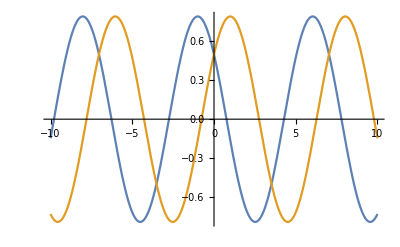

```mathematica
Plot[{x,y},{t,-10,10}]
```

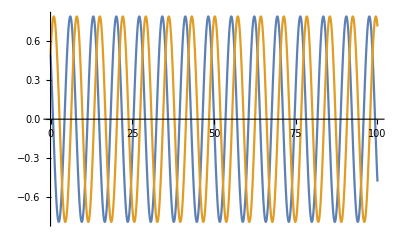

```mathematica
Plot[{x,y},{t,0,100}]
```

As t approaches ∞ the amplitude and period are the same, the functions just start at different t values.  This makes sense because the E term approaches 1 so has no effect on the size of the curve.

## Part 3: Other shapes

(i) Keeping the movable point on the curve to as close to (0.5,0.5) as you can, find values of a,b,c, & d that make your curve look a shape that is not a spiral going toward the origin or away from it, that is not a circle or oval, and looks like it neither would go through (0,0) nor orbit around it.

```mathematica
a3=1
b3=-1
c3=-.84
d3=-1
```

1

-1

-0.84

-1

(ii) Use DSolve (as with Part 1A) to find solution functions for x(t) and y(t).

```mathematica
Clear[x,y]
```

```mathematica
DSolve[{x'[t]==a3*x[t]+b3*y[t],y'[t]==c3*x[t]+d3*y[t],x[0]==0.5,y[0]==0.5},{x[t],y[t]},t]
```

{{x[t]→0.25 ⅇ^(-1.35647 t) (1.+1. ⅇ^(2.71293 t)),y[t]→-0.0891165 ⅇ^(-1.35647 t) (-6.61063+1. ⅇ^(2.71293 t))}}

(iii) Define Mathematica functions (call them x3 & y3) that represent your solutions.  Plot them together on the same set of axes with the horizontal axis representing t.  What is happening to the states of the differential equation as t→∞?

```mathematica
x=0.25 ⅇ^(-1.3565 t) (1+ⅇ^(2.7129t))
```

0.25 ⅇ^(-1.3565 t) (1+ⅇ^(2.7129 t))

```mathematica
y=-0.089 ⅇ^(-1.3565 t) (-6.6106+ⅇ^(2.7129t))
```

-0.089 ⅇ^(-1.3565 t) (-6.6106+ⅇ^(2.7129 t))

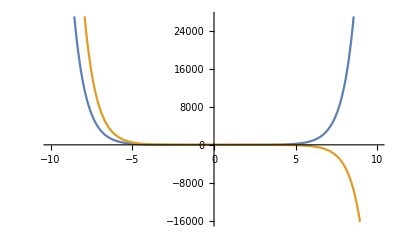

```mathematica
Plot[{x,y},{t,-10,10}]
```

```mathematica
Plot[{x,y},{t,0,100}]
```

-Graphics-

As t approaches ∞, the function gets exponentially larger.  The functions begin to diverge around t=4.  As t approaches ∞, x goes to ∞ and y goes to -∞.

## Part 4: Context

(i) Explain, in full sentences, the differences in how the solutions behave as t→∞ for Part 1A, 1B, 2, and 3.
Part 1A: The amplitude of the curve is increasing for both curves as t approaches ∞.  This makes sense because the only thing that is controlling the trend amplitude (overall) is the E term. The period is also decreasing.

Part 1B: The amplitude of the curves becomes very small as t approaches ∞.  This makes sense because the exponent on E is approaching 0.  The period also becomes longer as t approaches ∞.

Part 2: As t approaches ∞ the amplitude and period are the same, the functions just start at different t values.  This makes sense because the E term approaches 1 so has no effect on the size of the curve. 

Part 3: As t approaches ∞, the function gets exponentially larger.  The functions begin to diverge around t=4.  As t approaches ∞, x goes to ∞ and y goes to -∞.

(ii) In which situations is the parameteric solution curve attracted to the origin (or the critical point) and in which situations is the parametric solution repelled from the origin?  How can we connect these concepts with what we know about derivatives?  What happens if we use a point other than (0.5,0.5)?